# Лабораторная работа #8 Формальная справедливость

На практике мы решили функциональное уравнение:
		m(x/y)=(m(x))/(m(y)), x,y∈ℝ^+                                         (1)
доказав теорему: "Если функция m непрерывна в некоторой точке x_0∈ℝ^+, то все решения (1) имеют вид m(x)=x^p,p∈ℝ".

Обобщением модели (1) является уравнение:
		m(x/y)=с(m(x))/(m(y)), x,y∈ℝ^+,c>0                         (2)
решениями которого являются функции вида m(x)=c x^p,p∈ℝ. При этом функции m^*(x)=1/c m(x) будут решениями уравнения (1).

Домашнее задание:

1) Уравнения (1) и (2) допускают решения при p<0. Необходимо обосновать эти решения (желательно каким-нибудь реальным примером).

2) Решить задачу. Сотрудник A работает 25 лет и получает зарплату $2000000 в год, сотрудник B работает 16 лет и получает зарплату $60000 в год, сотрудник C работает 3 года и получает зарплату $40000 в год. С помощью модели (2) оценить справедливость зарплат. Если бы в задаче было только 2 сотрудника, то можно было бы подобрать параметры c и p так, чтобы данные задачи в точности лежали на графике одного из решений модели (2). В случае трех (и большего числа) сотрудников необходимо подобрать наилучшее решение m(x) методом наименьших квадратов ∑_(i=1)^n (y_i-m(x_i))^2→min, где x_i - стаж, y_i - зарплата.

3) Составить и решить задачу для функции двух переменных m(x_1,x_2), предполагая, что функции m_1(x_1)=m(x_1,x_2=const) и m_2(x_2)=m(x_1=const,x_2)будут удовлетворять уравнению (2).

4) Ответить,что было бы,если бы мы не могли утверждать,что m непрерывна?Как бы изменился ответ?

### 1) Уравнения (1) и (2) допускают решения при p<0. Необходимо обосновать эти решения (желательно каким-нибудь реальным примером).

Спортсмены. После определенного пика у них зарплата уменьшается.
Опасная работа

m(x)=c x^p,p∈ℝ
Если p <0, а параметр x изменяется от 0 до 1, то с уменьшением x, величина m(x) растет.
При приближении x к 1, величина  m(x) убывает.

Пусть x - доля пропущенных рабочих дней по отношению ко всем днем.
Если работник практически не имеет пропусков, то x близко к 0 (Пусть это величина X11).В таком случае x^p=1/x^-p-большое число.
Если работник имеет большую долю пропусков →1, то x→1 (Пусть это величина X22). В таком случае x^p=1/x^-p справа приближается к единице. 
Тогда определенно можно сказать, что c x11^p= m(x11)>m(x22)=c x22^p.

m(x)=c x^p,p∈ℝ
Если p <0, а параметр x > 1, то с увеличеним x, величина m(x) убывает, с уменьшением x, m(x) растет

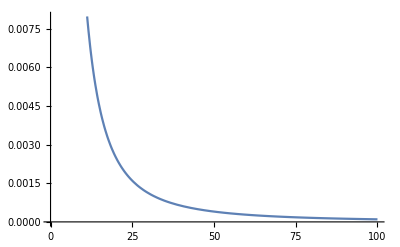

```mathematica
Plot[x^-2,{x,0,100},PlotRange->Automatic]
```

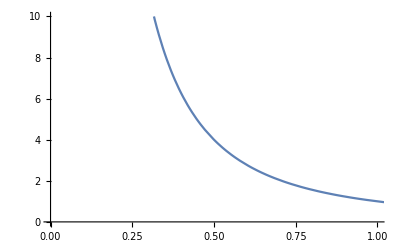

```mathematica
Plot[x^-2,{x,0,20},PlotRange->{{0,1},{0,10}}]
```

### 2) Решить задачу. Сотрудник A работает 25 лет и получает зарплату $2000000 в год, сотрудник B работает 16 лет и получает зарплату $60000 в год, сотрудник C работает 3 года и получает зарплату $40000 в год. С помощью модели (2) оценить справедливость зарплат. Если бы в задаче было только 2 сотрудника, то можно было бы подобрать параметры c и p так, чтобы данные задачи в точности лежали на графике одного из решений модели (2). В случае трех (и большего числа) сотрудников необходимо подобрать наилучшее решение m(x) методом наименьших квадратов ∑_(i=1)^n (y_i-m(x_i))^2→min, где x_i - стаж, y_i - зарплата.

```mathematica
x={25,16,3};
y={2000000,60000,40000};
```

```mathematica
m1[x_,p_]:=x^p
```

```mathematica
m2[x_,C_,p_]:=C x^p
```

```mathematica
min1=NMinimize[Sum[(y⟦i⟧-m1[x⟦i⟧,p])^2,{i,1,3}],p]
```

{4.41021×10^10,{p→4.50367}}

```mathematica
min2=NMinimize[Sum[(y⟦i⟧-m2[x⟦i⟧,c,p])^2,{i,1,3}],{p,c}]
```

{1.61371×10^9,{p→7.7236,c→0.0000319}}

```mathematica
p1=4.503673963929277;
p2=7.723599276448809;
c2=0.00003190002163504582;
```

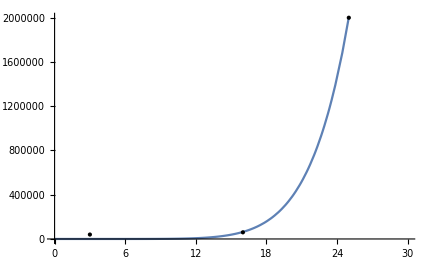

```mathematica
Show[Plot[m2[x,c2,p2],{x,0,30},PlotRange->{{0,30},{0,2000010}}],Graphics[Point[{{x⟦1⟧,y⟦1⟧},{x⟦2⟧,y⟦2⟧},{x⟦3⟧,y⟦3⟧}}]]]
```

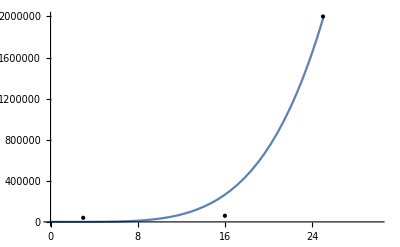

```mathematica
Show[Plot[m1[x,p1],{x,0,30},PlotRange->{{0,30},{0,2000100}}],Graphics[Point[{{x⟦1⟧,y⟦1⟧},{x⟦2⟧,y⟦2⟧},{x⟦3⟧,y⟦3⟧}}]]]
```

### 3) Составить и решить задачу для функции двух переменных m(x_1,x_2), предполагая, что функции m_1(x_1)=m(x_1,x_2=const) и m_2(x_2)=m(x_1=const,x_2)будут удовлетворять уравнению (2).

m(x/y)=с(m(x))/(m(y)), x,y∈ℝ^+,c>0

m(x)=c x^p,p∈ℝ


m(x,y)
m_x0(y)=m(x,y)|_(x=x0),
m_y0(x)=m(x,y)|_(y=y0),
Piecewise[{{m_x(y1/y2)=, C1(x)(m_x(y1))/(m_x(y2))}, {m_y(x1/x2)=, C2(y)(m_x(x1))/(m_x(x2))}}]

m_x(y)=C1(x) y^p1
m_y(x)=C2(y)x^p2



m(x1,x2)=c x1^p x2^p,p∈ℝ

m(x/y)=c(m(x))/(m(y))=c (c x^p)/(c y^p)=c x^p/y^p=c(x/y)^p=m(x/y)

m_1(x_1)=m(x1,x2=const)=c x1^p x2^p=(c x2^p) x1^p=m_1(x1)=C x1^p, где C = c x2^p
m_2(x_2)=m(x_1=const,x_2)=с x1^p x2^p = (c x1^p) x2^p =m_2(x2)=C x2^p, где C = c x1^p

m_1(x/y)=m(x/y,x2=const)=с(m(x))/(m(y))=с(m(x,x2=const))/(m(y,x2=const))=c ((c x2^p) x^p)/((c x2^p) y^p)=c x^p/y^p=m_1(x/y)
m_2(x/y)=m(x1=const,x/y)=с(m(x))/(m(y))=с(m(x1=const,x))/(m(x1=const,y))=c ((c x1^p) x^p)/((c x1^p) y^p)=c x^p/y^p=m_2(x/y)

```mathematica
m3[x_,x2_,C_,p_]:=C x^p x2^p
```

### 4) Ответить,что было бы,если бы мы не могли утверждать,что m непрерывна?Как бы изменился ответ?

Тогда не выполнялась бы теорема о непрерывности, поэтому мы не могли бы предполагать такое поведение функции.

Необходимое и достаточное условие представимости данной функции с любой степенью точности с помощью многочлена - непрерывность ее на этом отрезке. 
Функция, приближенно могущая быть представленной многочленом с любой степенью точности, есть предел равномерно сходящейся последовательности (значит, сумма входящегося ряда) многочленов, т.е непрерывных функций, и, следовательно, должна быть непрерывной. 
Это необходимое условие является и достаточным по теореме Вейерштрасса.